```mathematica
n=5;
```

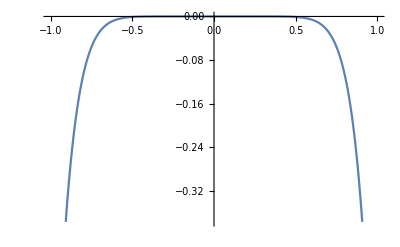

```mathematica
Plot[-x^{2n},{x,-1,1}]
```

```mathematica
$Assumptions = Im[Ee]==0&&Im[k]==0&&k>0&&Im[λ]==0&&λ>0&&Im[n]==0&&n∈Integers&&n>0&&Im[m]==0&&m>0&&Im[h]==0&&h>0;
```

```mathematica
k = Sqrt[2 m Ee]/h;
```

```mathematica
Eee[n_] :=Ee/.Solve[2*k*Integrate[Sqrt[1-(λ x^(2 n))/Ee],{x,0,(Ee/λ)^(1/(2 n))}]==(n+1/2) Pi,Ee][[1]]
```

Ee/.(2 √2 √(Ee m) ∫_0^((Ee/λ)^(1/2/n)) √(1-(x^(2 n) λ)/Ee)ⅆx)/h==(1/2+n) π

```mathematica
Integrate[Sqrt[1+(λ x^(2 n))/Ee],{x,0,(Abs[Ee]/λ)^(1/(2 n))}]
```

(√π (λ/Ee)^(-1/2/n) Gamma[1/2 (2+1/n)])/(2 Gamma[1/2 (3+1/n)])

```mathematica
E1[n_]:= 2*k*(√π (λ/Ee)^(-1/2/n) Gamma[1/2 (2+1/n)])/(2 Gamma[1/2 (3+1/n)]);
```

```mathematica
E1[n]
```

(√(Ee m) √(2 π) (λ/Ee)^(-1/2/n) Gamma[1/2 (2+1/n)])/(h Gamma[1/2 (3+1/n)])

```mathematica
Solve[E1[n]==(n+1/2) Pi,Ee]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[(√(Ee m) √(2 π) (λ/Ee)^(-1/2/n) Gamma[1/2 (2+1/n)])/(h Gamma[1/2 (3+1/n)])==(1/2+n) π,Ee]

```mathematica
Refine[Gamma[1/2 (2+1/n)]/Gamma[1/2 (3+1/n)],Assuming n∈Integers&&n>0]
```

Gamma[1/2 (2+1/n)]/Gamma[1/2 (3+1/n)]

```mathematica
N[Gamma[1/4]]
```

3.62561

```mathematica
N[(1/2)!]
```

0.886227

```mathematica
N[0.7^(1/4)]
```

0.914691

```mathematica
Sqrt[Sqrt[.7]]
```

0.914691

```mathematica
Limit[n/(n+1),n->∞]
```

1

```mathematica
Gamma[2]
```

1

```mathematica
Series[1/Sqrt[1+x],{x,a,4}]
```

1/(√(1+a))-(x-a)/(2 (1+a)^(3/2))+(3 (x-a)^2)/(8 (1+a)^(5/2))-(5 (x-a)^3)/(16 (1+a)^(7/2))+(35 (x-a)^4)/(128 (1+a)^(9/2))+O[x-a]^5

```mathematica
Series[Log[1+x],{x,0,3}]
```

x-x^2/2+x^3/3+O[x]^4

```mathematica
Integrate[Sqrt[1+(λ x^(2 n))/Ee],{x,0,(-Ee/λ)^(1/(2 n))},Assuming  Im[Ee]==0&&Ee<0&&0&&Im[λ]==0&&λ>0&&Im[n]==0&&n∈Integers&&n>0 ]
```

Integrate::ilim: Invalid integration variable or limit(s) in Assuming\ Im[Ee] == 0 && Ee < 0 && 0 && Im[λ] == 0 && λ > 0 && Im[n] == 0 && n ∈ Integers && n > 0.

$Assumptions::bass: 0 is not a well-formed assumption.

$Assumptions::cas: Warning: contradictory assumption(s) Im[Ee] == 0 && Ee < 0 && 0 && Im[λ] == 0 && λ > 0 && Im[n] == 0 && n ∈ Integers && n > 0 && Im[Ee] == 0 && √2\ Im[√Ee\ m/h] == 0 && √2\ √Ee\ m/h > 0 && Im[λ] == 0 && λ > 0 && Im[n] == 0 && n ∈ Integers && n > 0 && Im[m] == 0 && m > 0 && Im[h] == 0 && h > 0 encountered.

∫_0^((-Ee/λ)^(1/2/n)) √(1+(x^(2 n) λ)/Ee)ⅆx

```mathematica
ClearAll[Ee,a,λ,n]
```